## Wobbling motion for a simple triaxial rotator

```mathematica
moi1=10;
moi2=25;
moi3=50;
A1=1/(2moi1);
A2=1/(2moi2);
A3=1/(2moi3);
```

```mathematica
freq[I_]:=2*I*Sqrt[(A2-A3)(A1-A3)];
En[I_,n_]:=A3*I(I+1)+(n+1/2)freq[I];
ALPHA[I_]:=I(A2+A1-2A3);
BETA[I_]:=I(A2-A1);
```

### create lists with defined signatures

```mathematica
signatureBand[n_]:=Table[{i,En[i,n]},{i,If[EvenQ[n],0,1],40,2}];
```

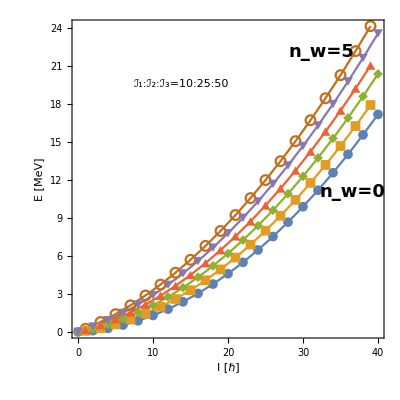

```mathematica
wobblingTable[n_]:=Table[signatureBand[i],{i,0,n,1}];
wobblingPlot[n_]:=ListPlot[wobblingTable[n],Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->1,FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","E [MeV]"},Epilog->{Inset[Framed[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:``"][moi1,moi2,moi3],Black,Bold,21,FontFamily->"Arial"]],Scaled[{0.35,0.8}]],Inset[Style["n_w=0",Black,18,Bold],Scaled[{0.9,0.46}]],Inset[Style["n_w=5",Black,18,Bold],Scaled[{0.8,0.9}]]},LabelStyle->{21,Bold,Black,FontFamily->"Arial"},PlotRange->All];
fig=wobblingPlot[5];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-even-A/wobbling-evenA.pdf",fig,ImageResolution->1200];
fig2=Plot[{freq[x],ALPHA[x],BETA[x]},{x,0,40},Frame->True,Axes->False,AspectRatio->1,FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","wobb"},LabelStyle->{21,Bold,Black,FontFamily->"Arial"},PlotRange->All,PlotLegends->Placed[{"ℏω_w","t_1","t_2"},Scaled[{0.8,0.4}]],PlotStyle->{{Red,Thick},{Blue,Thick},{Blue,Thick,Dashed}},Epilog->{Inset[Framed[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:``"][moi1,moi2,moi3],Black,Bold,21,FontFamily->"Arial"]],Scaled[{0.4,0.9}]]},PlotRange->Full];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-even-A/wobblingFreq-evenA.pdf",fig2,ImageResolution->1200];
fig=wobblingPlot[5]
```

```mathematica
(*PlotLegends->{Table[Style[StringTemplate["n_w=``"][i],12],{i,0,n}]},*)
```